```mathematica
(* 1) run Read data, Construct form functions, Reconstruct solution*)
```

### Read data

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop-Debug"}]]
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop_Qt_5_7_0_MinGW_32bit-Debug"}]]*)
```

/home/darksy/build-RKDG2D-Desktop-Debug

```mathematica
coeffs =Import["alphaCoeffs/2.000000","Table"];
mesh=Import["mesh2D","Table"];
```

```mathematica
Lx=mesh[[1,3]];
Ly=mesh[[2,3]];
nx=mesh[[3,3]];
ny=mesh[[4,3]];
hx=mesh[[5,3]];
hy=mesh[[6,3]];
numFF=mesh[[7,3]];
MeshCellArea=hx*hy;
MeshCellRcm=mesh[[9;;]];
nCells=Length@MeshCellRcm;
alpha=Table[Partition[coeffs[[i]],numFF],{i,1,nCells}];
```

#### Construct form functions

```mathematica
Phi0[n_,r_]:=1./(√MeshCellArea)
Phi10[n_,r_List]:=√(12./(hy hx^3))(r[[1]]-MeshCellRcm[[n,1]])
Phi11[n_,r_List]:=√(12./(hy^3 hx))(r[[2]]-MeshCellRcm[[n,2]])
Phi20[n_,r_List]:=√(180./(hy hx^5))((r[[1]]-MeshCellRcm[[n,1]])^2-hx^2/12)
Phi21[n_,r_List]:=√(144./(hy^3 hx^3))(r[[1]]-MeshCellRcm[[n,1]])(r[[2]]-MeshCellRcm[[n,2]])
Phi22[n_,r_List]:=√(180./(hy^5 hx))((r[[2]]-MeshCellRcm[[n,2]])^2-hy^2/12)

Phi[n_,r_List]:={Phi0[n,r],Phi10[n,r],Phi11[n,r],Phi20[n,r],Phi21[n,r],Phi22[n,r]}
```

#### Reconstruct solution

```mathematica
GetSol[alpha_,n_,numSol_,r_List]:=Sum[Phi[n,r][[i]]alpha[[n,numSol,i]],{i,numFF}];
```

```mathematica
GetSolDensity[alpha_,n_,numSol_]:=Module[{pts,anSol},(
pts={{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]+hy/2.0},
{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]+hy/2.0}};
anSol=Table[GetSol[alpha,n,numSol,pts[[i]]],{i,1,4}];
Return[Table[{pts[[i,1]],pts[[i,2]],anSol[[i]]},{i,1,4}]]
)];
GetSolGraphics[alpha_,n_,numSol_]:=Module[{pts,anSol},(
pts={{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]+hy/2.0},
{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]+hy/2.0}};
anSol=Table[GetSol[alpha,n,numSol,pts[[i]]],{i,1,4}];
Return[Polygon@Table[{pts[[i,1]],pts[[i,2]],anSol[[i]]3000000},{i,1,4}]]
)];
```

#### Compute integral

```mathematica
(MeshCellRcm[[i]]/.{i->10})-{Lx/2,Ly/2}
GetSol[alpha,i,1,MeshCellRcm[[i]]]/.i->200
```

Part::pkspec1: The expression i cannot be used as a part specification.

{3.6,-3.6}

Part::pkspec1: The expression i cannot be used as a part specification.

Part::partw: Part 200 of {{0.4,0.4},{1.2,0.4},{2,0.4},{2.8,0.4},{3.6,0.4},{4.4,0.4},{5.2,0.4},{6,0.4},{6.8,0.4},{7.6,0.4},{0.4,1.2},{1.2,1.2},{2,1.2},{2.8,1.2},{3.6,1.2},{4.4,1.2},{5.2,1.2},{6,1.2},{6.8,1.2},{7.6,1.2},{0.4,2},«10»,{1.2,2.8},{2,2.8},{2.8,2.8},{3.6,2.8},{4.4,2.8},{5.2,2.8},{6,2.8},{6.8,2.8},{7.6,2.8},{0.4,3.6},{1.2,3.6},{2,3.6},{2.8,3.6},{3.6,3.6},{4.4,3.6},{5.2,3.6},{6,3.6},{6.8,3.6},{7.6,3.6},«50»} does not exist.

GetSol[{{{0.8,-7.96531×10^-10,-7.96531×10^-10},{9.74726×10^-10,4.95798×10^-10,3.8881×10^-10},{9.74726×10^-10,3.8881×10^-10,4.95797×10^-10},{0,0,0},{2.,-2.75572×10^-9,-2.75572×10^-9}},{{0.8,-6.35761×10^-10,-5.8695×10^-10},{2.44692×10^-9,2.43251×10^-10,5.10445×10^-10},{2.7639×10^-9,2.33828×10^-10,1.2056×10^-9},{0,0,0},{2.,-2.25754×10^-9,-2.00884×10^-9}},{{0.8,1.61401×10^-9,1.74544×10^-9},{5.61769×10^-10,-9.72066×10^-10,-4.75275×10^-10},{1.79013×10^-9,-1.36036×10^-9,4.03655×10^-10},{0,0,0},{2.,5.47121×10^-9,6.18932×10^-9}},{{0.8,1.97683×10^-9,5.61119×10^-9},{-2.23967×10^-9,-6.15723×10^-10,-1.16769×10^-9},{-3.4078×10^-9,-1.79088×10^-9,-2.49854×10^-9},{0,0,0},{2.,7.98797×10^-9,1.99599×10^-8}},{{0.8,7.90145×10^-10,8.51832×10^-9},{-1.62571×10^-9,8.48741×10^-10,-5.75586×10^-10},{-8.87674×10^-9,-1.05116×10^-9,-5.41872×10^-9},{0,0,0},{2.,5.79832×10^-10,2.98551×10^-8}},{{0.8,-7.90145×10^-10,8.51832×10^-9},{1.62571×10^-9,8.48741×10^-10,5.75586×10^-10},{-8.87674×10^-9,1.05116×10^-9,-5.41872×10^-9},{0,0,0},{2.,-5.79833×10^-10,2.98551×10^-8}},{{0.8,-1.97683×10^-9,5.61119×10^-9},{2.23967×10^-9,-6.15723×10^-10,1.16769×10^-9},{-3.4078×10^-9,1.79088×10^-9,-2.49854×10^-9},{0,0,0},{2.,-7.98797×10^-9,1.99599×10^-8}},{{0.8,-1.61401×10^-9,1.74544×10^-9},{-5.61769×10^-10,-9.72066×10^-10,4.75275×10^-10},{1.79013×10^-9,1.36036×10^-9,4.03655×10^-10},{0,0,0},{2.,-5.47121×10^-9,6.18932×10^-9}},{{0.8,6.35761×10^-10,-5.8695×10^-10},{-2.44692×10^-9,2.43251×10^-10,-5.10445×10^-10},{2.7639×10^-9,-2.33828×10^-10,1.2056×10^-9},{0,0,0},{2.,2.25754×10^-9,-2.00884×10^-9}},{{0.8,7.96531×10^-10,-7.96531×10^-10},{-9.74726×10^-10,4.95798×10^-10,-3.8881×10^-10},{9.74726×10^-10,-3.8881×10^-10,4.95797×10^-10},{0,0,0},{2.,2.75572×10^-9,-2.75572×10^-9}},{{0.8,-5.8695×10^-10,-6.35761×10^-10},{2.7639×10^-9,1.2056×10^-9,2.33828×10^-10},{2.44692×10^-9,5.10445×10^-10,2.43251×10^-10},{0,0,0},{2.,-2.00884×10^-9,-2.25754×10^-9}},{{0.8,3.34231×10^-9,3.34231×10^-9},{1.70563×10^-10,-2.51752×10^-9,-2.11802×10^-9},{1.70563×10^-10,-2.11802×10^-9,-2.51752×10^-9},{0,0,0},{2.,1.14435×10^-8,1.14435×10^-8}},{{0.8,8.36462×10^-9,1.16126×10^-8},{-1.35785×10^-8,-4.12602×10^-9,-6.97304×10^-9},{-1.81647×10^-8,-7.9384×10^-9,-9.86665×10^-9},{0,0,0},{2.,2.94226×10^-8,4.03336×10^-8}},{{0.8,5.8283×10^-9,1.76898×10^-8},{-1.92095×10^-8,5.94042×10^-10,-7.64193×10^-9},{-4.73136×10^-8,-7.26592×10^-9,-1.80412×10^-8},{0,0,0},{2.,2.24886×10^-8,6.22847×10^-8}},{{0.8,1.68878×10^-9,1.9344×10^-8},{-8.64622×10^-9,4.8439×10^-9,-3.068×10^-9},{-6.90313×10^-8,-3.38986×10^-9,-2.27001×10^-8},{0,0,0},{2.,-3.66018×10^-10,6.63636×10^-8}},{{0.8,-1.68878×10^-9,1.9344×10^-8},{8.64622×10^-9,4.8439×10^-9,3.068×10^-9},{-6.90313×10^-8,3.38986×10^-9,-2.27001×10^-8},{0,0,0},{2.,3.66018×10^-10,6.63636×10^-8}},{{0.8,-5.8283×10^-9,1.76898×10^-8},{1.92095×10^-8,5.94042×10^-10,7.64193×10^-9},{-4.73136×10^-8,7.26592×10^-9,-1.80412×10^-8},{0,0,0},{2.,-2.24886×10^-8,6.22847×10^-8}},{{0.8,-8.36462×10^-9,1.16126×10^-8},{1.35785×10^-8,-4.12602×10^-9,6.97304×10^-9},{-1.81647×10^-8,7.9384×10^-9,-9.86665×10^-9},{0,0,0},{2.,-2.94226×10^-8,4.03336×10^-8}},{{0.8,-3.34231×10^-9,3.34231×10^-9},{-1.70563×10^-10,-2.51752×10^-9,2.11802×10^-9},{1.70563×10^-10,2.11802×10^-9,-2.51752×10^-9},{0,0,0},{2.,-1.14435×10^-8,1.14435×10^-8}},{{0.8,5.8695×10^-10,-6.35761×10^-10},{-2.7639×10^-9,1.2056×10^-9,-2.33828×10^-10},{2.44692×10^-9,-5.10445×10^-10,2.43251×10^-10},{0,0,0},{2.,2.00884×10^-9,-2.25754×10^-9}},{{0.8,1.74544×10^-9,1.61401×10^-9},{1.79013×10^-9,4.03655×10^-10,-1.36036×10^-9},{5.61769×10^-10,-4.75275×10^-10,-9.72066×10^-10},{0,0,0},{2.,6.18932×10^-9,5.47121×10^-9}},{{0.8,1.16126×10^-8,8.36462×10^-9},{-1.81647×10^-8,-9.86665×10^-9,-7.9384×10^-9},{-1.35785×10^-8,-6.97304×10^-9,-4.12602×10^-9},{0,0,0},{2.,4.03336×10^-8,2.94226×10^-8}},{{0.8,1.1285×10^-8,1.1285×10^-8},{-5.11112×10^-8,-6.59185×10^-9,-1.28592×10^-8},{-5.11112×10^-8,-1.28592×10^-8,-6.59185×10^-9},{0,0,0},{2.,4.19341×10^-8,4.19341×10^-8}},{{0.8,-1.78538×10^-9,-5.66343×10^-10},{-4.59811×10^-8,6.6676×10^-9,-7.3046×10^-9},{-8.23281×10^-8,-4.76087×10^-9,-1.47411×10^-9},{0,0,0},{2.,-3.59058×10^-9,2.79744×10^-9}},{{0.8,-3.08316×10^-9,-1.38806×10^-8},{-1.55835×10^-8,9.38725×10^-9,-1.17459×10^-9},{-9.17934×10^-8,-6.81329×10^-10,6.58819×10^-9},{0,0,0},{2.,-2.94987×10^-8,-5.02526×10^-8}},{{0.8,3.08316×10^-9,-1.38806×10^-8},{1.55835×10^-8,9.38725×10^-9,1.17459×10^-9},{-9.17934×10^-8,6.81329×10^-10,6.58819×10^-9},{0,0,0},{2.,2.94987×10^-8,-5.02526×10^-8}},{{0.8,1.78538×10^-9,-5.66343×10^-10},{4.59811×10^-8,6.6676×10^-9,7.3046×10^-9},{-8.23281×10^-8,4.76087×10^-9,-1.47411×10^-9},{0,0,0},{2.,3.59058×10^-9,2.79744×10^-9}},{{0.8,-1.1285×10^-8,1.1285×10^-8},{5.11112×10^-8,-6.59185×10^-9,1.28592×10^-8},{-5.11112×10^-8,1.28592×10^-8,-6.59185×10^-9},{0,0,0},{2.,-4.19341×10^-8,4.19341×10^-8}},{{0.8,-1.16126×10^-8,8.36462×10^-9},{1.81647×10^-8,-9.86665×10^-9,7.9384×10^-9},{-1.35785×10^-8,6.97304×10^-9,-4.12602×10^-9},{0,0,0},{2.,-4.03336×10^-8,2.94226×10^-8}},{{0.8,-1.74544×10^-9,1.61401×10^-9},{-1.79013×10^-9,4.03655×10^-10,1.36036×10^-9},{5.61768×10^-10,4.75275×10^-10,-9.72066×10^-10},{0,0,0},{2.,-6.18932×10^-9,5.47121×10^-9}},{{0.8,5.61119×10^-9,1.97683×10^-9},{-3.4078×10^-9,-2.49854×10^-9,-1.79088×10^-9},{-2.23967×10^-9,-1.16769×10^-9,-6.15723×10^-10},{0,0,0},{2.,1.99599×10^-8,7.98797×10^-9}},{{0.8,1.76898×10^-8,5.8283×10^-9},{-4.73136×10^-8,-1.80412×10^-8,-7.26592×10^-9},{-1.92095×10^-8,-7.64193×10^-9,5.94041×10^-10},{0,0,0},{2.,6.22847×10^-8,2.24886×10^-8}},{{0.8,-5.66343×10^-10,-1.78538×10^-9},{-8.23281×10^-8,-1.47411×10^-9,-4.76087×10^-9},{-4.59811×10^-8,-7.3046×10^-9,6.6676×10^-9},{0,0,0},{2.,2.79744×10^-9,-3.59058×10^-9}},{{0.8,-2.2305×10^-8,-2.2305×10^-8},{-3.93177×10^-8,1.70742×10^-8,7.80233×10^-9},{-3.93177×10^-8,7.80233×10^-9,1.70742×10^-8},{0,0,0},{2.,-8.78826×10^-8,-8.78826×10^-8}},{{0.8,-9.98753×10^-9,-3.30389×10^-8},{-2.30997×10^-9,4.93969×10^-9,6.8626×10^-9},{-1.12352×10^-8,6.28227×10^-9,2.51017×10^-8},{0,0,0},{2.,-8.40439×10^-8,-1.57378×10^-7}},{{0.8,9.98753×10^-9,-3.30389×10^-8},{2.30997×10^-9,4.93969×10^-9,-6.8626×10^-9},{-1.12352×10^-8,-6.28227×10^-9,2.51017×10^-8},{0,0,0},{2.,8.40439×10^-8,-1.57378×10^-7}},{{0.8,2.2305×10^-8,-2.2305×10^-8},{3.93177×10^-8,1.70742×10^-8,-7.80233×10^-9},{-3.93177×10^-8,-7.80233×10^-9,1.70742×10^-8},{0,0,0},{2.,8.78826×10^-8,-8.78826×10^-8}},{{0.8,5.66343×10^-10,-1.78538×10^-9},{8.23281×10^-8,-1.47411×10^-9,4.76087×10^-9},{-4.59811×10^-8,7.3046×10^-9,6.6676×10^-9},{0,0,0},{2.,-2.79744×10^-9,-3.59058×10^-9}},{{0.8,-1.76898×10^-8,5.8283×10^-9},{4.73136×10^-8,-1.80412×10^-8,7.26592×10^-9},{-1.92095×10^-8,7.64193×10^-9,5.94041×10^-10},{0,0,0},{2.,-6.22847×10^-8,2.24886×10^-8}},{{0.8,-5.61119×10^-9,1.97683×10^-9},{3.4078×10^-9,-2.49854×10^-9,1.79088×10^-9},{-2.23967×10^-9,1.16769×10^-9,-6.15723×10^-10},{0,0,0},{2.,-1.99599×10^-8,7.98797×10^-9}},{{0.8,8.51832×10^-9,7.90145×10^-10},{-8.87674×10^-9,-5.41872×10^-9,-1.05116×10^-9},{-1.62571×10^-9,-5.75586×10^-10,8.48741×10^-10},{0,0,0},{2.,2.98551×10^-8,5.79832×10^-10}},{{0.8,1.9344×10^-8,1.68878×10^-9},{-6.90313×10^-8,-2.27001×10^-8,-3.38986×10^-9},{-8.64622×10^-9,-3.068×10^-9,4.8439×10^-9},{0,0,0},{2.,6.63636×10^-8,-3.66018×10^-10}},{{0.8,-1.38806×10^-8,-3.08316×10^-9},{-9.17934×10^-8,6.58819×10^-9,-6.81329×10^-10},{-1.55835×10^-8,-1.17459×10^-9,9.38725×10^-9},{0,0,0},{2.,-5.02526×10^-8,-2.94987×10^-8}},{{0.8,-3.30389×10^-8,-9.98753×10^-9},{-1.12352×10^-8,2.51017×10^-8,6.28227×10^-9},{-2.30997×10^-9,6.8626×10^-9,4.93969×10^-9},{0,0,0},{2.,-1.57378×10^-7,-8.40439×10^-8}},{{0.8,-9.063×10^-9,-9.063×10^-9},{1.83345×10^-8,-3.57102×10^-9,4.50798×10^-9},{1.83345×10^-8,4.50798×10^-9,-3.57102×10^-9},{0,0,0},{2.,-1.21323×10^-7,-1.21323×10^-7}},{{0.8,9.063×10^-9,-9.063×10^-9},{-1.83345×10^-8,-3.57102×10^-9,-4.50798×10^-9},{1.83345×10^-8,-4.50798×10^-9,-3.57102×10^-9},{0,0,0},{2.,1.21323×10^-7,-1.21323×10^-7}},{{0.8,3.30389×10^-8,-9.98753×10^-9},{1.12352×10^-8,2.51017×10^-8,-6.28227×10^-9},{-2.30997×10^-9,-6.8626×10^-9,4.93969×10^-9},{0,0,0},{2.,1.57378×10^-7,-8.40439×10^-8}},{{0.8,1.38806×10^-8,-3.08316×10^-9},{9.17934×10^-8,6.58819×10^-9,6.81329×10^-10},{-1.55835×10^-8,1.17459×10^-9,9.38725×10^-9},{0,0,0},{2.,5.02526×10^-8,-2.94987×10^-8}},{{0.8,-1.9344×10^-8,1.68878×10^-9},{6.90313×10^-8,-2.27001×10^-8,3.38986×10^-9},{-8.64622×10^-9,3.068×10^-9,4.8439×10^-9},{0,0,0},{2.,-6.63636×10^-8,-3.66018×10^-10}},{{0.8,-8.51832×10^-9,7.90145×10^-10},{8.87674×10^-9,-5.41872×10^-9,1.05116×10^-9},{-1.62571×10^-9,5.75586×10^-10,8.48741×10^-10},{0,0,0},{2.,-2.98551×10^-8,5.79833×10^-10}},{{0.8,8.51832×10^-9,-7.90145×10^-10},{-8.87674×10^-9,-5.41872×10^-9,1.05116×10^-9},{1.62571×10^-9,5.75586×10^-10,8.48741×10^-10},{0,0,0},{2.,2.98551×10^-8,-5.79833×10^-10}},{{0.8,1.9344×10^-8,-1.68878×10^-9},{-6.90313×10^-8,-2.27001×10^-8,3.38986×10^-9},{8.64622×10^-9,3.068×10^-9,4.8439×10^-9},{0,0,0},{2.,6.63636×10^-8,3.66018×10^-10}},{{0.8,-1.38806×10^-8,3.08316×10^-9},{-9.17934×10^-8,6.58819×10^-9,6.81329×10^-10},{1.55835×10^-8,1.17459×10^-9,9.38725×10^-9},{0,0,0},{2.,-5.02526×10^-8,2.94987×10^-8}},{{0.8,-3.30389×10^-8,9.98753×10^-9},{-1.12352×10^-8,2.51017×10^-8,-6.28227×10^-9},{2.30997×10^-9,-6.8626×10^-9,4.93969×10^-9},{0,0,0},{2.,-1.57378×10^-7,8.40439×10^-8}},{{0.8,-9.063×10^-9,9.063×10^-9},{1.83345×10^-8,-3.57102×10^-9,-4.50798×10^-9},{-1.83345×10^-8,-4.50798×10^-9,-3.57102×10^-9},{0,0,0},{2.,-1.21323×10^-7,1.21323×10^-7}},{{0.8,9.063×10^-9,9.063×10^-9},{-1.83345×10^-8,-3.57102×10^-9,4.50798×10^-9},{-1.83345×10^-8,4.50798×10^-9,-3.57102×10^-9},{0,0,0},{2.,1.21323×10^-7,1.21323×10^-7}},{{0.8,3.30389×10^-8,9.98753×10^-9},{1.12352×10^-8,2.51017×10^-8,6.28227×10^-9},{2.30997×10^-9,6.8626×10^-9,4.93969×10^-9},{0,0,0},{2.,1.57378×10^-7,8.40439×10^-8}},{{0.8,1.38806×10^-8,3.08316×10^-9},{9.17934×10^-8,6.58819×10^-9,-6.81329×10^-10},{1.55835×10^-8,-1.17459×10^-9,9.38725×10^-9},{0,0,0},{2.,5.02526×10^-8,2.94987×10^-8}},{{0.8,-1.9344×10^-8,-1.68878×10^-9},{6.90313×10^-8,-2.27001×10^-8,-3.38986×10^-9},{8.64622×10^-9,-3.068×10^-9,4.8439×10^-9},{0,0,0},{2.,-6.63636×10^-8,3.66017×10^-10}},{{0.8,-8.51832×10^-9,-7.90145×10^-10},{8.87674×10^-9,-5.41872×10^-9,-1.05116×10^-9},{1.62571×10^-9,-5.75586×10^-10,8.48741×10^-10},{0,0,0},{2.,-2.98551×10^-8,-5.79833×10^-10}},{{0.8,5.61119×10^-9,-1.97683×10^-9},{-3.4078×10^-9,-2.49854×10^-9,1.79088×10^-9},{2.23967×10^-9,1.16769×10^-9,-6.15723×10^-10},{0,0,0},{2.,1.99599×10^-8,-7.98797×10^-9}},{{0.8,1.76898×10^-8,-5.8283×10^-9},{-4.73136×10^-8,-1.80412×10^-8,7.26592×10^-9},{1.92095×10^-8,7.64193×10^-9,5.94042×10^-10},{0,0,0},{2.,6.22847×10^-8,-2.24886×10^-8}},{{0.8,-5.66343×10^-10,1.78538×10^-9},{-8.23281×10^-8,-1.47411×10^-9,4.76087×10^-9},{4.59811×10^-8,7.3046×10^-9,6.6676×10^-9},{0,0,0},{2.,2.79744×10^-9,3.59058×10^-9}},{{0.8,-2.2305×10^-8,2.2305×10^-8},{-3.93177×10^-8,1.70742×10^-8,-7.80233×10^-9},{3.93177×10^-8,-7.80233×10^-9,1.70742×10^-8},{0,0,0},{2.,-8.78826×10^-8,8.78826×10^-8}},{{0.8,-9.98753×10^-9,3.30389×10^-8},{-2.30997×10^-9,4.93969×10^-9,-6.8626×10^-9},{1.12352×10^-8,-6.28227×10^-9,2.51017×10^-8},{0,0,0},{2.,-8.40439×10^-8,1.57378×10^-7}},{{0.8,9.98753×10^-9,3.30389×10^-8},{2.30997×10^-9,4.93969×10^-9,6.8626×10^-9},{1.12352×10^-8,6.28227×10^-9,2.51017×10^-8},{0,0,0},{2.,8.40439×10^-8,1.57378×10^-7}},{{0.8,2.2305×10^-8,2.2305×10^-8},{3.93177×10^-8,1.70742×10^-8,7.80233×10^-9},{3.93177×10^-8,7.80233×10^-9,1.70742×10^-8},{0,0,0},{2.,8.78826×10^-8,8.78826×10^-8}},{{0.8,5.66343×10^-10,1.78538×10^-9},{8.23281×10^-8,-1.47411×10^-9,-4.76087×10^-9},{4.59811×10^-8,-7.3046×10^-9,6.6676×10^-9},{0,0,0},{2.,-2.79744×10^-9,3.59058×10^-9}},{{0.8,-1.76898×10^-8,-5.8283×10^-9},{4.73136×10^-8,-1.80412×10^-8,-7.26592×10^-9},{1.92095×10^-8,-7.64193×10^-9,5.94042×10^-10},{0,0,0},{2.,-6.22847×10^-8,-2.24886×10^-8}},{{0.8,-5.61119×10^-9,-1.97683×10^-9},{3.4078×10^-9,-2.49854×10^-9,-1.79088×10^-9},{2.23967×10^-9,-1.16769×10^-9,-6.15723×10^-10},{0,0,0},{2.,-1.99599×10^-8,-7.98797×10^-9}},{{0.8,1.74544×10^-9,-1.61401×10^-9},{1.79013×10^-9,4.03655×10^-10,1.36036×10^-9},{-5.61769×10^-10,4.75275×10^-10,-9.72066×10^-10},{0,0,0},{2.,6.18932×10^-9,-5.47121×10^-9}},{{0.8,1.16126×10^-8,-8.36462×10^-9},{-1.81647×10^-8,-9.86665×10^-9,7.9384×10^-9},{1.35785×10^-8,6.97304×10^-9,-4.12602×10^-9},{0,0,0},{2.,4.03336×10^-8,-2.94226×10^-8}},{{0.8,1.1285×10^-8,-1.1285×10^-8},{-5.11112×10^-8,-6.59185×10^-9,1.28592×10^-8},{5.11112×10^-8,1.28592×10^-8,-6.59185×10^-9},{0,0,0},{2.,4.19341×10^-8,-4.19341×10^-8}},{{0.8,-1.78538×10^-9,5.66343×10^-10},{-4.59811×10^-8,6.6676×10^-9,7.3046×10^-9},{8.23281×10^-8,4.76087×10^-9,-1.47411×10^-9},{0,0,0},{2.,-3.59058×10^-9,-2.79744×10^-9}},{{0.8,-3.08316×10^-9,1.38806×10^-8},{-1.55835×10^-8,9.38725×10^-9,1.17459×10^-9},{9.17934×10^-8,6.81329×10^-10,6.58819×10^-9},{0,0,0},{2.,-2.94987×10^-8,5.02526×10^-8}},{{0.8,3.08316×10^-9,1.38806×10^-8},{1.55835×10^-8,9.38725×10^-9,-1.17459×10^-9},{9.17934×10^-8,-6.81329×10^-10,6.58819×10^-9},{0,0,0},{2.,2.94987×10^-8,5.02526×10^-8}},{{0.8,1.78538×10^-9,5.66343×10^-10},{4.59811×10^-8,6.6676×10^-9,-7.3046×10^-9},{8.23281×10^-8,-4.76087×10^-9,-1.47411×10^-9},{0,0,0},{2.,3.59058×10^-9,-2.79744×10^-9}},{{0.8,-1.1285×10^-8,-1.1285×10^-8},{5.11112×10^-8,-6.59185×10^-9,-1.28592×10^-8},{5.11112×10^-8,-1.28592×10^-8,-6.59185×10^-9},{0,0,0},{2.,-4.19341×10^-8,-4.19341×10^-8}},{{0.8,-1.16126×10^-8,-8.36462×10^-9},{1.81647×10^-8,-9.86665×10^-9,-7.9384×10^-9},{1.35785×10^-8,-6.97304×10^-9,-4.12602×10^-9},{0,0,0},{2.,-4.03336×10^-8,-2.94226×10^-8}},{{0.8,-1.74544×10^-9,-1.61401×10^-9},{-1.79013×10^-9,4.03655×10^-10,-1.36036×10^-9},{-5.61769×10^-10,-4.75275×10^-10,-9.72066×10^-10},{0,0,0},{2.,-6.18932×10^-9,-5.47121×10^-9}},{{0.8,-5.8695×10^-10,6.35761×10^-10},{2.7639×10^-9,1.2056×10^-9,-2.33828×10^-10},{-2.44692×10^-9,-5.10445×10^-10,2.43251×10^-10},{0,0,0},{2.,-2.00884×10^-9,2.25754×10^-9}},{{0.8,3.34231×10^-9,-3.34231×10^-9},{1.70563×10^-10,-2.51752×10^-9,2.11802×10^-9},{-1.70563×10^-10,2.11802×10^-9,-2.51752×10^-9},{0,0,0},{2.,1.14435×10^-8,-1.14435×10^-8}},{{0.8,8.36462×10^-9,-1.16126×10^-8},{-1.35785×10^-8,-4.12602×10^-9,6.97304×10^-9},{1.81647×10^-8,7.9384×10^-9,-9.86665×10^-9},{0,0,0},{2.,2.94226×10^-8,-4.03336×10^-8}},{{0.8,5.8283×10^-9,-1.76898×10^-8},{-1.92095×10^-8,5.94041×10^-10,7.64193×10^-9},{4.73136×10^-8,7.26592×10^-9,-1.80412×10^-8},{0,0,0},{2.,2.24886×10^-8,-6.22847×10^-8}},{{0.8,1.68878×10^-9,-1.9344×10^-8},{-8.64622×10^-9,4.8439×10^-9,3.068×10^-9},{6.90313×10^-8,3.38986×10^-9,-2.27001×10^-8},{0,0,0},{2.,-3.66018×10^-10,-6.63636×10^-8}},{{0.8,-1.68878×10^-9,-1.9344×10^-8},{8.64622×10^-9,4.8439×10^-9,-3.068×10^-9},{6.90313×10^-8,-3.38986×10^-9,-2.27001×10^-8},{0,0,0},{2.,3.66017×10^-10,-6.63636×10^-8}},{{0.8,-5.8283×10^-9,-1.76898×10^-8},{1.92095×10^-8,5.94041×10^-10,-7.64193×10^-9},{4.73136×10^-8,-7.26592×10^-9,-1.80412×10^-8},{0,0,0},{2.,-2.24886×10^-8,-6.22847×10^-8}},{{0.8,-8.36462×10^-9,-1.16126×10^-8},{1.35785×10^-8,-4.12602×10^-9,-6.97304×10^-9},{1.81647×10^-8,-7.9384×10^-9,-9.86665×10^-9},{0,0,0},{2.,-2.94226×10^-8,-4.03336×10^-8}},{{0.8,-3.34231×10^-9,-3.34231×10^-9},{-1.70563×10^-10,-2.51752×10^-9,-2.11802×10^-9},{-1.70563×10^-10,-2.11802×10^-9,-2.51752×10^-9},{0,0,0},{2.,-1.14435×10^-8,-1.14435×10^-8}},{{0.8,5.8695×10^-10,6.35761×10^-10},{-2.7639×10^-9,1.2056×10^-9,2.33828×10^-10},{-2.44692×10^-9,5.10445×10^-10,2.43251×10^-10},{0,0,0},{2.,2.00884×10^-9,2.25754×10^-9}},{{0.8,-7.96531×10^-10,7.96531×10^-10},{9.74726×10^-10,4.95797×10^-10,-3.8881×10^-10},{-9.74726×10^-10,-3.8881×10^-10,4.95797×10^-10},{0,0,0},{2.,-2.75572×10^-9,2.75572×10^-9}},{{0.8,-6.35761×10^-10,5.8695×10^-10},{2.44692×10^-9,2.43251×10^-10,-5.10445×10^-10},{-2.7639×10^-9,-2.33828×10^-10,1.2056×10^-9},{0,0,0},{2.,-2.25754×10^-9,2.00884×10^-9}},{{0.8,1.61401×10^-9,-1.74544×10^-9},{5.61769×10^-10,-9.72066×10^-10,4.75275×10^-10},{-1.79013×10^-9,1.36036×10^-9,4.03655×10^-10},{0,0,0},{2.,5.47121×10^-9,-6.18932×10^-9}},{{0.8,1.97683×10^-9,-5.61119×10^-9},{-2.23967×10^-9,-6.15723×10^-10,1.16769×10^-9},{3.4078×10^-9,1.79088×10^-9,-2.49854×10^-9},{0,0,0},{2.,7.98797×10^-9,-1.99599×10^-8}},{{0.8,7.90145×10^-10,-8.51832×10^-9},{-1.62571×10^-9,8.48741×10^-10,5.75586×10^-10},{8.87674×10^-9,1.05116×10^-9,-5.41872×10^-9},{0,0,0},{2.,5.79832×10^-10,-2.98551×10^-8}},{{0.8,-7.90145×10^-10,-8.51832×10^-9},{1.62571×10^-9,8.48741×10^-10,-5.75586×10^-10},{8.87674×10^-9,-1.05116×10^-9,-5.41872×10^-9},{0,0,0},{2.,-5.79833×10^-10,-2.98551×10^-8}},{{0.8,-1.97683×10^-9,-5.61119×10^-9},{2.23967×10^-9,-6.15723×10^-10,-1.16769×10^-9},{3.4078×10^-9,-1.79088×10^-9,-2.49854×10^-9},{0,0,0},{2.,-7.98797×10^-9,-1.99599×10^-8}},{{0.8,-1.61401×10^-9,-1.74544×10^-9},{-5.61768×10^-10,-9.72066×10^-10,-4.75275×10^-10},{-1.79013×10^-9,-1.36036×10^-9,4.03655×10^-10},{0,0,0},{2.,-5.47121×10^-9,-6.18932×10^-9}},{{0.8,6.35761×10^-10,5.8695×10^-10},{-2.44692×10^-9,2.43251×10^-10,5.10445×10^-10},{-2.7639×10^-9,2.33828×10^-10,1.2056×10^-9},{0,0,0},{2.,2.25754×10^-9,2.00884×10^-9}},{{0.8,7.96531×10^-10,7.96531×10^-10},{-9.74726×10^-10,4.95797×10^-10,3.8881×10^-10},{-9.74726×10^-10,3.8881×10^-10,4.95797×10^-10},{0,0,0},{2.,2.75572×10^-9,2.75572×10^-9}}},200,1,{{0.4,0.4},{1.2,0.4},{2,0.4},{2.8,0.4},{3.6,0.4},{4.4,0.4},{5.2,0.4},{6,0.4},{6.8,0.4},{7.6,0.4},{0.4,1.2},{1.2,1.2},{2,1.2},{2.8,1.2},{3.6,1.2},{4.4,1.2},{5.2,1.2},{6,1.2},{6.8,1.2},{7.6,1.2},{0.4,2},{1.2,2},{2,2},{2.8,2},{3.6,2},{4.4,2},{5.2,2},{6,2},{6.8,2},{7.6,2},{0.4,2.8},{1.2,2.8},{2,2.8},{2.8,2.8},{3.6,2.8},{4.4,2.8},{5.2,2.8},{6,2.8},{6.8,2.8},{7.6,2.8},{0.4,3.6},{1.2,3.6},{2,3.6},{2.8,3.6},{3.6,3.6},{4.4,3.6},{5.2,3.6},{6,3.6},{6.8,3.6},{7.6,3.6},{0.4,4.4},{1.2,4.4},{2,4.4},{2.8,4.4},{3.6,4.4},{4.4,4.4},{5.2,4.4},{6,4.4},{6.8,4.4},{7.6,4.4},{0.4,5.2},{1.2,5.2},{2,5.2},{2.8,5.2},{3.6,5.2},{4.4,5.2},{5.2,5.2},{6,5.2},{6.8,5.2},{7.6,5.2},{0.4,6},{1.2,6},{2,6},{2.8,6},{3.6,6},{4.4,6},{5.2,6},{6,6},{6.8,6},{7.6,6},{0.4,6.8},{1.2,6.8},{2,6.8},{2.8,6.8},{3.6,6.8},{4.4,6.8},{5.2,6.8},{6,6.8},{6.8,6.8},{7.6,6.8},{0.4,7.6},{1.2,7.6},{2,7.6},{2.8,7.6},{3.6,7.6},{4.4,7.6},{5.2,7.6},{6,7.6},{6.8,7.6},{7.6,7.6}}⟦200⟧]

```mathematica
hx hy Sum[GetSol[alpha,i,1,MeshCellRcm[[i]]],{i,1,nCells}]
```

64.

```mathematica
16.0004592
```

16.0005

```mathematica
16.000465920000014 -16.000460079999883
```

5.84×10^-6

```mathematica
16.000460079999883
```

16.0005

```mathematica
16.0004592 -16.000460079999883
```

-8.8×10^-7

```mathematica
16.00156879999998
```

16.0016

#### Draw solution Graphics

```mathematica
Graphics3D@Table[GetSolGraphics[alpha,i,1],{i,1,nCells}]
```

-Graphics3D-

#### Draw in diag

```mathematica
diagPoints=Table[MeshCellRcm[[i]]-0.5{hx,hy},{i,1,nCells,nx+1}]~Join~{MeshCellRcm[[nCells]]+0.5{hx,hy}};
diagV=diagPoints[[2]]-diagPoints[[1]];
diagH=Norm[diagV,2];
diagX=Table[i*diagH,{i,0,Length[diagPoints]-1}];
diagVal=Table[{GetSol[alpha,i,1,MeshCellRcm[[i]]-0.5{hx,hy}],GetSol[alpha,i,1,MeshCellRcm[[i]]+0.5{hx,hy}]},{i,1,nCells,nx+1}];
```

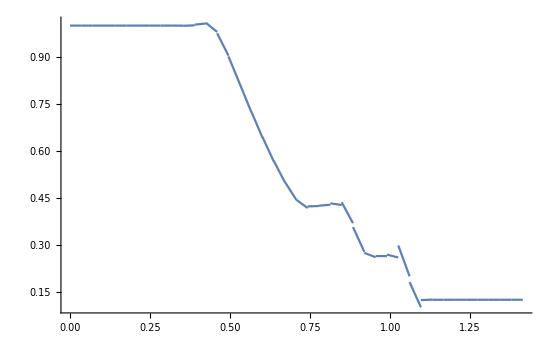

```mathematica
ggg=Show[Table[ListLinePlot[{{diagX[[i]],diagVal[[i,1]]},{diagX[[i+1]],diagVal[[i,2]]}}],{i,1,Length[diagX]-1}],PlotRange->All]
```

Draw in diag cell average

```mathematica
Norm[MeshCellRcm[[1]],2]
```

0.0176777

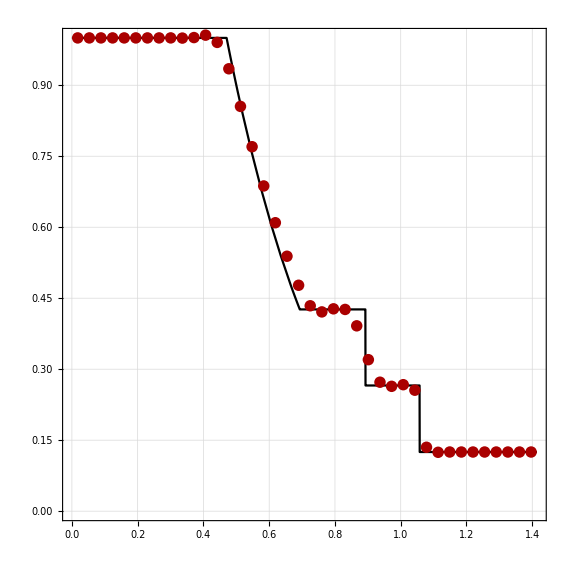

```mathematica
mcc=Table[MeshCellRcm[[i]],{i,1,nCells,nx+1}];
mcy=Table[GetSol[alpha,i,1,MeshCellRcm[[i]]],{i,1,nCells,nx+1}];
mcx=Table[Norm[mcc[[i]],2],{i,Length[mcc]}];
exactDiag=Plot[ρ[x-(√2-1)/2,0.2],{x,0,√2},PlotStyle->Black,Exclusions->None];
grsode=Show[exactDiag,ListPlot[Transpose@{mcx,mcy},
PlotStyle->{Darker[Red],PointSize[0.0145]}],AspectRatio->1,
Frame->True,
FrameStyle->Black,
GridLines->Automatic,
LabelStyle->Directive[12,FontFamily->"Times"]]
```

```mathematica
Export["LLF+WENOS.png",grsode,ImageResolution->300]
```

LLF+WENOS.png

#### Draw in X or Y direction

```mathematica
bou=MeshCellRcm[[All,1]]-hx/2;
```

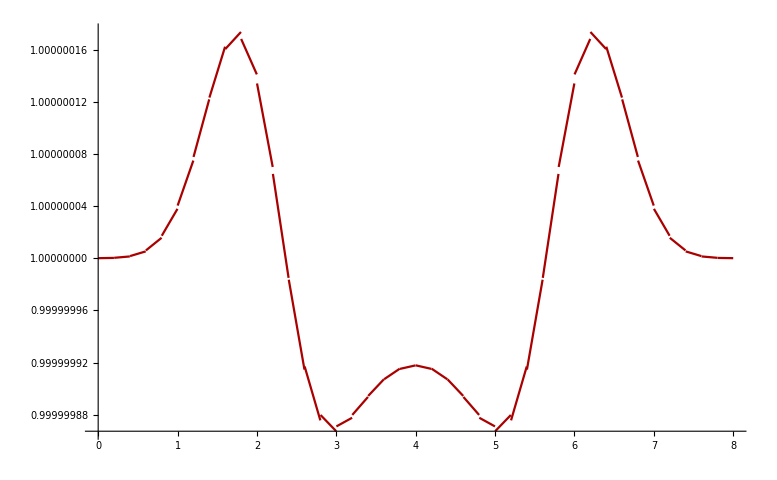

```mathematica
funVis1D[y_]:=Piecewise[Table[{GetSol[alpha,i,1,{0,y}],MeshCellRcm[[i,2]]-hy/2.0 < y <MeshCellRcm[[i,2]]+hy/2.0},{i,1,nCells}]];
funVis1D[x_]:=Piecewise[Table[{(GetSol[alpha,i,1,{x,(Lx+hx)/2}]/1),MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,nx ny/2+1,nx ny/2+nx}]];
fig2=Plot[funVis1D[x],{x,0,Lx},Exclusions->bou,PlotPoints->100,PlotRange->All,PlotStyle->Darker[Red]]
```

```mathematica
getPressure[x_,i_]:=(1.4-1)(GetSol[alpha,i,5,{x,(Lx+hx)/2}]-1/2((GetSol[alpha,i,2,{x,(Lx+hx)/2}]^2+GetSol[alpha,i,3,{x,(Lx+hx)/2}]^2+GetSol[alpha,i,4,{x,(Lx+hx)/2}]^2)/GetSol[alpha,i,1,{x,(Lx+hx)/2}]))
```

```mathematica
getEnthalpy[x_,i_]:=(getPressure[x,i]+GetSol[alpha,i,5,{x,(Lx+hx)/2}])/GetSol[alpha,i,1,{x,(Lx+hx)/2}]
```

```mathematica
funVisp1D[x_]:=Piecewise[Table[{(getPressure[x,i]),MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,nx ny/2+1,nx ny/2+nx}]];
grp=Plot[funVisp1D[x],{x,0,12},Exclusions->bou,PlotPoints->100,PlotRange->All,PlotStyle->Darker[Red]];
```

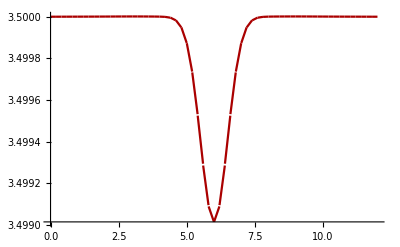

```mathematica
funVish1D[x_]:=Piecewise[Table[{(getEnthalpy[x,i]),MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,nx ny/2+1,nx ny/2+nx}]];
grh=Plot[funVish1D[x],{x,0,12},Exclusions->bou,PlotPoints->100,PlotRange->All,PlotStyle->Darker[Red]]
```

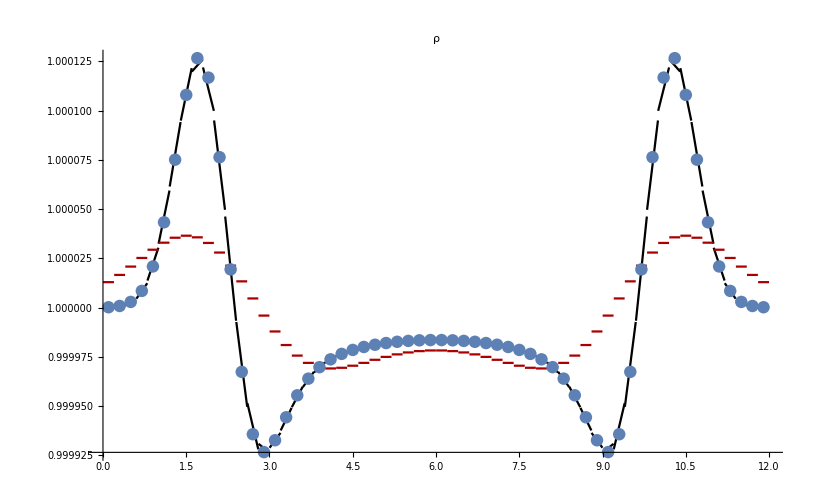

```mathematica
Show[fig1,fig2,ListPlot[dataAnCenterRhoEqP,PlotRange->All],PlotLabel->"ρ",LabelStyle->Directive[{Black,12}],AxesStyle->Black]
```

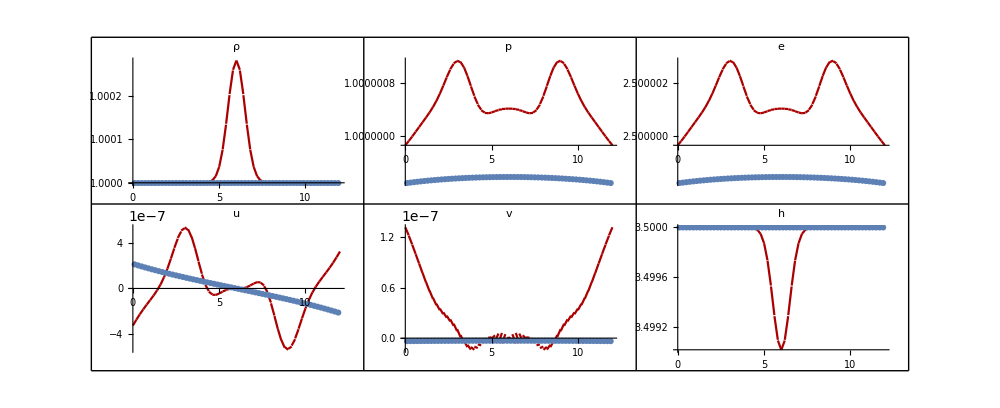

```mathematica
full=GraphicsGrid[{{Show[fig2,ListPlot[dataAnCenterRhoEqP,PlotRange->All],PlotLabel->"ρ",LabelStyle->Directive[{Black,12}],AxesStyle->Black],Show[grp,ListPlot[dataAnCenterRhoEqP,PlotRange->All],PlotLabel->"p",LabelStyle->Directive[{Black,12}],AxesStyle->Black],
Show[fig2e,ListPlot[dataAnCenterE,PlotRange->All],PlotLabel->"e",
LabelStyle->Directive[{Black,12}],AxesStyle->Black]},
{Show[fig2U,ListPlot[dataAnCenterU,PlotRange->All],PlotLabel->"u",
LabelStyle->Directive[{Black,12}],AxesStyle->Black],Show[fig2V,ListPlot[dataAnCenterV,PlotRange->All],PlotLabel->"v",
LabelStyle->Directive[{Black,12}],AxesStyle->Black],
Show[grh,ListPlot[dataAnCenterH,PlotRange->All],PlotLabel->"h",
LabelStyle->Directive[{Black,12}],AxesStyle->Black]}},
Frame->All,ImageSize->1000]
```

```mathematica
Export["t=20.jpg",full,ImageResolution->150]
```

t=20.jpg

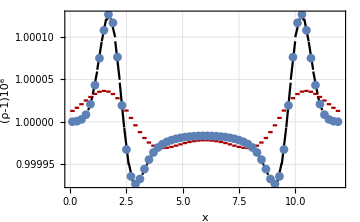

```mathematica
grd=Table[MeshCellRcm[[i,1]]-hx/2,{i,1,nx}]~Join~{MeshCellRcm[[nx,1]]+hx/2};
ee=Show[fig1,fig2,ListPlot[dataAnCenterRhoEqP,PlotRange->All,PlotMarkers->Automatic],
Frame->True,
GridLines->{grd,Automatic},
ImageSize->Medium,
LabelStyle->Directive[Black,12,FontFamily->"Times"],
FrameLabel->{"x","(ρ-1)10^6"}]
```

```mathematica
Export["LF_t=2.png",ee,ImageResolution->300]
```

LF_t=2.png

#### Draw Sode problem

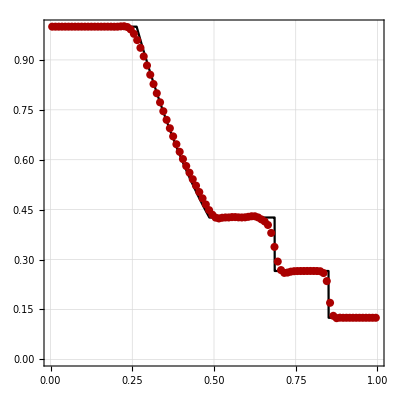

```mathematica
exact=Plot[ρ[x,0.2],{x,0,1},PlotStyle->Black,Exclusions->None];
grsode=Show[exact,ListPlot[Table[{MeshCellRcm[[i,1]],GetSol[alpha,i,1,MeshCellRcm[[i]]]},{i,1,nx}],PlotStyle->{Darker[Red],PointSize[0.0145]}],AspectRatio->1,
Frame->True,
FrameStyle->Black,
GridLines->Automatic,
LabelStyle->Directive[12,FontFamily->"Times"]]
```

```mathematica
grsodeDiag=Show[exact,ListPlot[Table[{MeshCellRcm[[i,1]],GetSol[alpha,i,1,MeshCellRcm[[i]]]},{i,1,nx}],PlotStyle->{Darker[Red],PointSize[0.0145]}],AspectRatio->1,
Frame->True,
FrameStyle->Black,
GridLines->Automatic,
LabelStyle->Directive[12,FontFamily->"Times"]]
```

```mathematica
Export["HLLC+WENOS+Everywhere.png",grsode,ImageResolution->300]
```

HLLC+WENOS+Everywhere.png

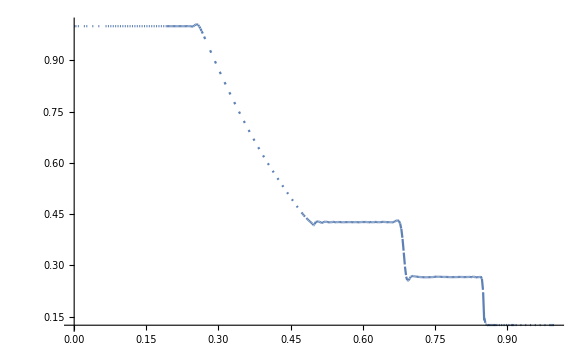

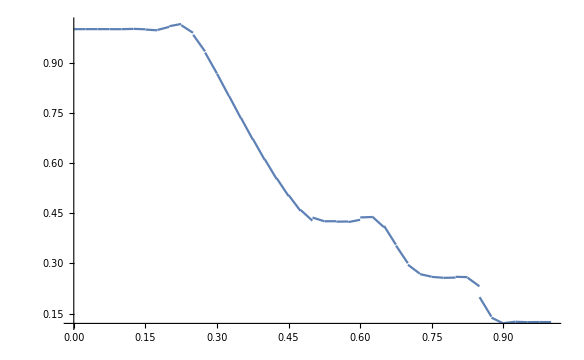

```mathematica
troubledCells={50,51}+1
funVis1DLim[x_]:=Piecewise[Table[{GetSol[alpha,i,1,{x,0}],MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,troubledCells}]];
```

{51,52}

```mathematica
trb=Plot[funVis1DLim[x],{x,0,1},PlotStyle->Red,Exclusions->bou,PlotPoints->200];
```

Part::partw: Part 51 of {{0.0125,0.25},{0.0375,0.25},{0.0625,0.25},{0.0875,0.25},{0.1125,0.25},{0.1375,0.25},{0.1625,0.25},{0.1875,0.25},{0.2125,0.25},{0.2375,0.25},{0.2625,0.25},{0.2875,0.25},«16»,{0.7125,0.25},{0.7375,0.25},{0.7625,0.25},{0.7875,0.25},{0.8125,0.25},{0.8375,0.25},{0.8625,0.25},{0.8875,0.25},{0.9125,0.25},{0.9375,0.25},{0.9625,0.25},{0.9875,0.25}} does not exist.

Part::partw: Part 51 of {{{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan}},{{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan}},«37»,{{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Show[fig,trb]
```

-Graphics-

#### Draw density plot

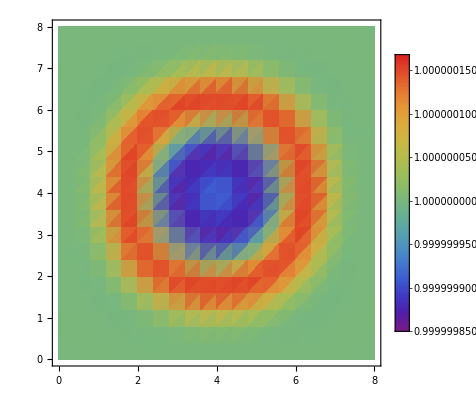

```mathematica
dd=ListDensityPlot[Table[GetSolDensity[alpha,i,1],{i,1,nCells}],AspectRatio->1/1,PlotRange->All,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```